```mathematica
audio=ExampleData[{"Audio","ThaiBells"}]
```

```mathematica
Audio[File["ExampleData/car.mp3"]]
```

```mathematica
ExampleData["Audio"]
```

{{Audio,Apollo11ReturnSafely},{Audio,Apollo11SmallStep},{Audio,BalloonPop},{Audio,Bee},{Audio,Bird},{Audio,BlackcapWarbler},{Audio,Cat},{Audio,Cello},{Audio,CelloScale},{Audio,ChurchBell},{Audio,Clapping},{Audio,CreakyDoor},{Audio,Crowd},{Audio,DogBark},{Audio,Drums},{Audio,FemaleVoice},{Audio,Flute},{Audio,FluteScale},{Audio,FogHorn},{Audio,IRMaesHowe},{Audio,IRRailwayTunnel},{Audio,IRSportsCenter},{Audio,IRStairway},{Audio,IRStAndrewsChurch},{Audio,IRStMarysChurch},{Audio,IRYorkMinsterChurch},{Audio,Laughing},{Audio,MaleVoice},{Audio,NoisyTalk},{Audio,Piano},{Audio,PianoScale},{Audio,PowerSupply},{Audio,Scream},{Audio,SubwayTrain},{Audio,Sword},{Audio,ThaiBells},{Audio,Walking},{Audio,Water},{Audio,Wind}}

```mathematica
DynamicModule[
			{p={2,2},q={3,3}},
			DynamicWrapper[
				Graphics[
						{Point[q],
						Locator[Dynamic[p]],
						Line[{q,Dynamic[p]}]
						},
						PlotRange->{{0,4},{0,4}},
						Frame->True
						],
				If[
					EuclideanDistance[q,p]<0.1,
					EmitSound[Sound[SoundNote[]]]
					]
				]
			]
```

```mathematica
Deploy[DynamicModule[{p={0,1}},Graphics[{Circle[],Locator[Dynamic[p,(p=Normalize[#])&]]},PlotRange->1.5]]]
```

```mathematica
ConstrainedLocatorToLine::usage="ConstrainedLocatorToLine[locator, ptA, ptB] will return new locator coordinates that have been projected onto the line defined by ptA and ptB. All quantities are in the form of list coordinates: {x, y}.";
SyntaxInformation[ConstrainedLocatorToLine]={"ArgumentsPattern"->{_,_,_}};
ConstrainedLocatorToLine[{xloc_,yloc_},{xA_,yA_},{xB_,yB_}]:={xA-((xA-xB) (xA^2+xB xloc-xA (xB+xloc)+(yA-yB) (yA-yloc)))/((xA-xB)^2+(yA-yB)^2),((xA-xB) (-xB yA+xloc (yA-yB)+xA yB)+(yA-yB)^2 yloc)/((xA-xB)^2+(yA-yB)^2)};
```

```mathematica
DynamicModule[{ptA={-1,-1},ptB={1,1},locator={0,0},constrain},constrain[loc_,pa_,pb_]:=(locator=ConstrainedLocatorToLine[loc,pa,pb]);
Graphics[{Dynamic@{Line[{ptA,ptB}]},Locator[Dynamic[ptA,(ptA=#;constrain[locator,ptA,ptB])&]],Locator[Dynamic[ptB,(ptB=#;constrain[locator,ptA,ptB])&]],Locator[Dynamic[locator,(locator=#;constrain[locator,ptA,ptB])&]]},PlotRange->2,ImageSize->250]]
```

```mathematica
DynamicModule[{ptA={-1,-1},ptB={1,1},locator={0,0},constrain},constrain[loc_,pa_,pb_]:=(locator=ConstrainedLocatorToLine[loc,pa,pb]);
Graphics[{Dynamic@{Line[{ptA,ptB}]},Locator[Dynamic[locator,(locator=#;constrain[locator,ptA,ptB])&]]},PlotRange->2,ImageSize->250]]
```

```mathematica
circles=Table[Circle[{0,0},r],{r,1,15,2}];
lines=Table[Line[{{-15 Cos[the],-15 Sin[the]},{15 Cos[the],15 Sin[the]}}],{the,0,Pi,Pi/6}];
grid=RegionUnion[circles,lines];
```

```mathematica
DynamicModule[{pt={4,0}},LocatorPane[Dynamic[pt,(pt=RegionNearest[grid,#])&],Graphics[{Lighter@Lighter@Blue,circles,lines}]]]
```

```mathematica
lines=Line[{{-1 ,-1},{1,1}}];
```

```mathematica
DynamicModule[
			{pt={{0,0},{0.2,0.2},{0.4,0.4}}},
			LocatorPane[
				Dynamic[pt,(pt=RegionNearest[lines,#])&],
				Graphics[{Lighter@Lighter@Blue,lines}]
			]
]
```

```mathematica
DynamicModule[
			{p={0.6,0.6},pt={{0,0},{0.2,0.2},{0.4,0.4}},lines=Line[{{-1 ,-1},{1,1}}]},
			DynamicWrapper[
						LocatorPane[
								Dynamic[pt,(pt=RegionNearest[lines,#])&],
								Graphics[
										{Lighter@Lighter@Blue,lines},
										Frame->True
										]
								],
						If[
							EuclideanDistance[pt[[1]],p]<0.1||EuclideanDistance[pt[[2]],p]<0.1||EuclideanDistance[pt[[3]],p]<0.1
							,
							EmitSound[Sound[SoundNote[]]]
						]
			]
]
```

```mathematica
Manipulate[
DynamicModule[
			{p={1-t,1-t},pt={{-0.4,-0.4},{0.2,0.2},{0.4,0.4}},lines=Line[{{-1 ,-1},{1,1}}]},
			DynamicWrapper[
						LocatorPane[
								Dynamic[pt,(pt=RegionNearest[lines,#])&],
								Graphics[
										
										{PointSize[Large],Point[p],Lighter@Lighter@Blue,lines},
										Frame->True
										]
								],
						If[
							EuclideanDistance[pt[[1]],p]<0.05||EuclideanDistance[pt[[2]],p]<0.05||EuclideanDistance[pt[[3]],p]<0.05
							,
							EmitSound[Sound[SoundNote[]]]
						]
			]
	],

{t,0,2},
SaveDefinitions->True
]
```

```mathematica
DynamicModule[
			{pt={{-0.4,-0.4},{0.2,0.2},{0.4,0.4}},lines=Line[{{-1 ,-1},{1,1}}]},
			Manipulate[
			DynamicWrapper[
						LocatorPane[
								Dynamic[pt,(pt=RegionNearest[lines,#])&],
								Graphics[
										
										{PointSize[Large],Point[{1-t,1-t}],Lighter@Lighter@Blue,lines},
										Frame->True
										]
								],
						If[
							EuclideanDistance[pt[[1]],{1-t,1-t}]<0.05||EuclideanDistance[pt[[2]],{1-t,1-t}]<0.05||EuclideanDistance[pt[[3]],{1-t,1-t}]<0.05
							,
							EmitSound[Sound[SoundNote[]]]
						]
			]
	,

{t,0,2},
SaveDefinitions->True]
]
```

```mathematica
AudioCapture["bells2.wav"]
```

```mathematica
bells=;
```

```mathematica
AudioCapture["bellsplane.wav"]
```

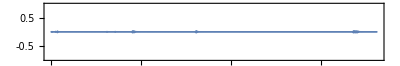

```mathematica
AudioPlot[bells]
```

```mathematica
sp=Spectrogram[bells]
```

-Graphics-

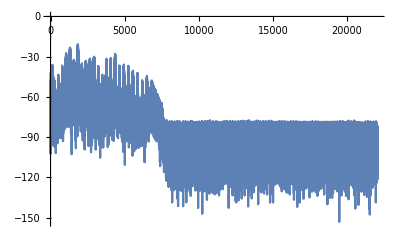

```mathematica
p=Periodogram[bells]
```